### Computational problem

#### Tracing functions with text

```mathematica
a
```

```mathematica
(*creates list of points given a function, bounds, and the number of points that you want*)
createPointLst[func_, lower_, upper_, points_]:=Module[
{xspace=(upper-lower)/(points-1)},
Table[{x, func[x]}, {x,lower, upper, xspace}]
]
```

```mathematica
f[x_]:=x^2
```

```mathematica
createPointLst[f, 0, 5, 5]
```

{{0,0},{5/4,25/16},{5/2,25/4},{15/4,225/16},{5,25}}

```mathematica
h[x_]:=Sin[x]
```

```mathematica
createPointLst[h, 0, 2π, 10]
```

{{0,0},{(2 π)/9,Sin[(2 π)/9]},{(4 π)/9,Cos[π/18]},{(2 π)/3,(√3)/2},{(8 π)/9,Sin[π/9]},{(10 π)/9,-Sin[π/9]},{(4 π)/3,-(√3)/2},{(14 π)/9,-Cos[π/18]},{(16 π)/9,-Sin[(2 π)/9]},{2 π,0}}

```mathematica
(*splits up string into each letter and the point it needs to be at*)
prepareTextDisplay[text_, ptLst_, color_]:=Module[
{cnt=1, list},
Table[
(*Text is needed to plot later*)
Text[Style[StringTake[text, {cnt}], Large, color], ptLst[[cnt]]],
{cnt, StringLength@text}
]
]
```

```mathematica
ptLst ={{0,0},{0.3, 0},{0.6,0.2},{1.2,0.9},{1.5, 0.3}, {2, -.8}, {2.5, -1.9}};
```

```mathematica
newlist=prepareTextDisplay["Gatton",ptLst, Green]
```

{Text[G,{0,0}],Text[a,{0.3,0}],Text[t,{0.6,0.2}],Text[t,{1.2,0.9}],Text[o,{1.5,0.3}],Text[n,{2,-0.8}]}

```mathematica
FullForm[newlist[[1]]]
```

Text[Style["G",Large,RGBColor[0,1,0]],List[0,0]]

```mathematica
ptLst2={{1,1}, {2,2}, {3,3}, {4,4}, {5,5}, {6,6}};
newlist2=prepareTextDisplay["Linear", ptLst2, Green]
```

{Text[L,{1,1}],Text[i,{2,2}],Text[n,{3,3}],Text[e,{4,4}],Text[a,{5,5}],Text[r,{6,6}]}

```mathematica
(*displays information from primitive list in preareTextDisplay*)
displayText[primitiveLst_]:=
Graphics[primitiveLst]
```

```mathematica
displayText[newlist]
```

-Graphics-

```mathematica
displayText[newlist2]
```

-Graphics-

```mathematica
(*plots function with the letters from the function*)
horizontalTrace[func_, text_, lower_, upper_, color_]:=Module[{pointlist},
pointlist=createPointLst[func, lower, upper, StringLength[text]];
Show[Plot[func[x], {x, lower, upper}, PlotRange->All], 
(*display letter list*)
displayText[prepareTextDisplay[text, pointlist, color]], PlotRange->All 
]
]
```

```mathematica
g[x_]:=E^-x Sin[x]
```

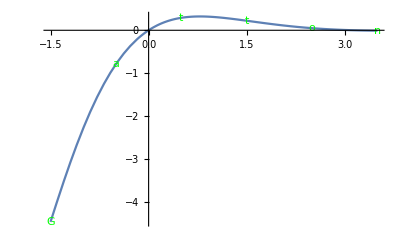

```mathematica
horizontalTrace[g, "Gatton", -1.5, 3.5, Green]
```

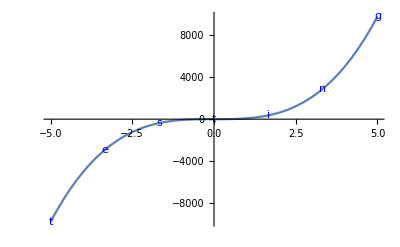

```mathematica
z[x_]:=78 x^3+3x-1
horizontalTrace[z, "testing", -5, 5, Blue]
```

```mathematica
b
```

```mathematica
(*finds number of spaces each line needs to reflect the y value of a func*)
createSpaceLst[func_,lower_, upper_,lines_, maxBlanks_]:=Module[
(*gets points from creatPointList funtion*)
{pointList=createPointLst[func, lower, upper, lines],yList},
yList=Table[{pointList[[cnt, 2]]}, {cnt, Length@pointList}];
(*the equation is a proportion of the y corrdinate to the maxBlanks, and scales accordingly such that the maximum number of spaces is maxBlanks*)
Flatten@Table[Round[(yList[[pt]]-Min[yList])/(Max[yList]-Min[yList])*maxBlanks], {pt, Length@yList}]
]
```

```mathematica
gv[x_]:=0.5 x^2
```

```mathematica
createSpaceLst[gv, -1.5, 3, 8, 10]
```

{2,1,0,0,1,3,6,10}

```mathematica
hv[x_]:=Cos[4x]
createSpaceLst[hv, 0, π/2,8, 7]
```

{7,6,2,0,0,2,6,7}

```mathematica
(*prints text after offset characters*)
offsetPrint[offset_,character_,text_]:=Module[
{str="", i=1},
While[i≤offset,
(*concatenates character*)
str=str<>character;
i++];
(*concatenates text*)
str=str<>text;
Print[str]
]
```

```mathematica
offsetPrint[5, " ", "Please give me an A"]
```

Please give me an A

```mathematica
offsetPrint[7, "@", "Hello"]
```

@@@@@@@Hello

```mathematica
(*is passed a list of spaces and prints the text out after each space element*)
verticalTrace[func_, text_, lines_, lower_, upper_, maxBlanks_]:=Module[{yList=createSpaceLst[func, lower, upper, lines, maxBlanks], cnt=1},
While[cnt≤lines,
offsetPrint[yList[[cnt]], " ", text];
cnt++
]
]
```

```mathematica
verticalTrace[gv, "Parabola", 8, -1.5, 3, 10]
```

Parabola

Parabola

Parabola

«5 more identical outputs»

```mathematica
ty[x_]:=x^3
```

```mathematica
verticalTrace[ty, "cubic", 6, -10, 10, 7]
```

cubic

cubic

cubic

«3 more identical outputs»